```mathematica
Quit[];
```

{-Graphics-,-Graphics-}

11.6733+1.9957 x

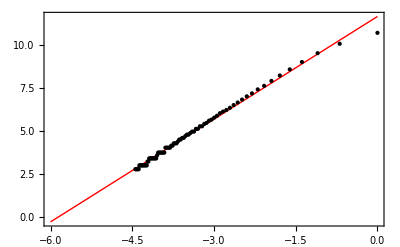

```mathematica
img=-Graphics-(**);
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

```mathematica
Manipulate[ImageSubtract[Binarize[Img,LowerBinThreshold],Binarize[Img,UpperBinThreshold]],{LowerBinThreshold,0,UpperBinThreshold,.01},{UpperBinThreshold,LowerBinThreshold,1,.01}]
```

```mathematica
Manipulate[Binarize[Img,UpperBinThreshold],{UpperBinThreshold,0,1,.01}]
```

```mathematica
points={{8.95373,1.31065},{9.72871,1.47645},{10.2513,1.5973},{10.752,1.71612},{11.09411,1.798596},{11.536752,1.9071},{11.79334,1.971147 }};
pointsDim1={{1,1.31065},{2,1.47645},{3,1.5973},{5,1.71612},{7,1.798596},{12,1.9071},{22,1.971147 }};
pointsDim0={{1,8.95373},{2,9.72871},{3,10.2513},{5,10.752},{7,11.09411},{12,11.536752},{22,11.79334}};
Row[ListPlot[points,ImageSize->300,PlotMarkers->{Automatic,Large},AspectRatio->1,AxesOrigin->Automatic],ListPlot[pointsDim1,ImageSize->300,PlotMarkers->{Automatic,Large},AspectRatio->1,AxesOrigin->Automatic],ListPlot[pointsDim0,ImageSize->300,PlotMarkers->{Automatic,Large},AspectRatio->1,AxesOrigin->Automatic]]
```

```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];

memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

ImageSizeLocal=450;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};

For[i=1,i≤mtxw,i++,{
For[j=1,j≤Round[mtxh/2],j++,{
memoryTem=data1[[(i-1)*mtxh+j,3]];
data1[[(i-1)*mtxh+j,3]]=data1[[(i-1)*mtxh+(mtxh+1-j),3]];
data1[[(i-1)*mtxh+(mtxh+1-j),3]]=memoryTem;
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]
ListDensityPlot[data1,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0] 

Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[i,{i,mtxw*mtxh}],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

data2=data1; Clear[data1];
arrenged=Array[{#/#}&,{redw,redh,3}];
For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{
arrenged[[i,j,1]]=(i-0.5)*sw;
arrenged[[i,j,2]]=sh*(j-0.5);

arrenged[[i,j,3]]=Sum[data2[[Mask43[[i,j,a]],3]],{a,sw*sh}]*(1/(sw*sh));
noiseF[x_,av_]:=x-av;
For[a:=1,a≤(sw*sh),a++,{data2[[Mask43[[i,j,a]],3]]=(1/TechError)*noiseF[data2[[Mask43[[i,j,a]],3]],arrenged[[i,j,3]]];
If[Abs@data2[[Mask43[[i,j,a]],3]]>FilterForErrorMagnitude1,data2[[Mask43[[i,j,a]],3]]=0];
}]

  }]

}]

Clear[arrenged,Mask43];
(*For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>Temperaturethreshold,data2[[i,3]]=0]]
For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>0.1,data2[[i,3]]=Temperaturethreshold]]*)

ListDensityPlot[data2,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]
(*ListPointPlot3D[data1,ColorFunction->Function[{x,y,z},Hue[-z]]]*)

Clear[data2];
```

{,}

C:\A\Notes\PRG\W\gjIR000110.dat File exists

CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}

-Graphics-

CheckPoint#2  - excellent

-Graphics-

```mathematica
ClearAll["Global'*"];
Needs["PlotLegends`"](* PlotLegends is now obsolete*) 
Evaluate[{FileNameSetter[Dynamic[datafilename1]],Dynamic[datafilename1]}] 
If[FileExistsQ[datafilename1],Print["File exists "datafilename1],Print["This File does not exist"];Quit[]];
 data1=Import[datafilename1];

memoryTem=0;
mtxw=320; mtxh=240; sw=4; sh=3; 
redw=Round[mtxw/sw]; redh=Round[mtxh/sh];
Temperaturethreshold=.3;  showmesh=False;TechError=0.05;
FilterForErrorMagnitude1=1;

ImageSizeLocal=450;
colorsGoody={RGBColor[0.05374,0,0.333],RGBColor[0.0979,0,0.467],RGBColor[0,0,1],RGBColor[0.2,1,0.96],RGBColor[0,0.93,0.07519],RGBColor[1,1,0],RGBColor[1,0,0],Darker[RGBColor[1,0,0],.4]};

For[i=1,i≤mtxw,i++,{
For[j=1,j≤Round[mtxh/2],j++,{
memoryTem=data1[[(i-1)*mtxh+j,3]];
data1[[(i-1)*mtxh+j,3]]=data1[[(i-1)*mtxh+(mtxh+1-j),3]];
data1[[(i-1)*mtxh+(mtxh+1-j),3]]=memoryTem;
}]
}]
Print["CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}"]
ListDensityPlot[data1,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0] 

Mask43=ArrayReshape[Transpose@ArrayReshape[ArrayReshape[Transpose@ArrayReshape[Table[i,{i,mtxw*mtxh}],{mtxw,mtxh}],{redw,mtxh,sw}],{mtxh,redw,sw}],{redw,redh,sw*sh}];

If[Mask43[[redw,redh,sw*sh]]==mtxw*mtxh,Print["CheckPoint#2  - excellent"],Print["CheckPoint#2 - failed!"]]

data2=data1; Clear[data1];
arrenged=Array[{#/#}&,{redw,redh,3}];
For[i=1,i<=Length[arrenged],i++,{
For[j=1,j<=Length[arrenged[[i]]],j++,{
arrenged[[i,j,1]]=(i-0.5)*sw;
arrenged[[i,j,2]]=sh*(j-0.5);

arrenged[[i,j,3]]=Sum[data2[[Mask43[[i,j,a]],3]],{a,sw*sh}]*(1/(sw*sh));
noiseF[x_,av_]:=x-av;
For[a:=1,a≤(sw*sh),a++,{data2[[Mask43[[i,j,a]],3]]=(1/TechError)*noiseF[data2[[Mask43[[i,j,a]],3]],arrenged[[i,j,3]]];
If[Abs@data2[[Mask43[[i,j,a]],3]]>FilterForErrorMagnitude1,data2[[Mask43[[i,j,a]],3]]=0]  }]

  }]

}]

Clear[arrenged,Mask43];
(*For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>Temperaturethreshold,data2[[i,3]]=0]]
For[i=1,i<=Length[data2],i++,If[Abs[data2[[i,3]]]>0.1,data2[[i,3]]=Temperaturethreshold]]*)

ListDensityPlot[data2,PlotRange->All,ColorFunction->(*colorsGoody*)GrayLevel,Mesh->showmesh,Mesh->{redw-1,redh-1},ImageSize->ImageSizeLocal,ClippingStyle->Automatic,PlotLegends->Automatic,ColorFunctionScaling->True,InterpolationOrder->0]
(*ListPointPlot3D[data1,ColorFunction->Function[{x,y,z},Hue[-z]]]*)

Clear[data2];
```

{,}

C:\A\Notes\PRG\W\gjIR000110.dat File exists

CheckPoint#1  - the matrix rotation was done - {1..320,1..240}->{1..320,240..1}}

-Graphics-

CheckPoint#2  - excellent

-Graphics-

Reduced noise contourPlot. (If only |noise magnitude| > 0.05 K -  IR-imager detection possibility!)

-Graphics-

Reduced noise contourPlot.(If only |noise magnitude| <0.05 K-IR-imager detection possibility!)

-Graphics-

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

{-Graphics-,-Graphics-}

10.3922+1.85057 x

-Graphics-

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

```mathematica
img=-Graphics-;
{Binarize[img],iEdge=EdgeDetect[Binarize[img]]}
MinS=Floor[Min[ImageDimensions[iEdge]]/2];

data=ParallelTable[{1/size,Total[Sign/@(Total[#,2]&/@(ImageData/@Flatten[ImagePartition[iEdge,size]]))]},{size,1,MinS/2,1}];
line=Fit[Log[data],{1,x},x]
Plot[line,{x,-6,0},Epilog->Point[Log[data]],PlotStyle->Red,Frame->True,Axes->False]
```

{-Graphics-,-Graphics-}

10.6575+1.92318 x

-Graphics-